```mathematica
4/τ∑_(n=nMin)^nMax (ⅇ^(-(-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^2]) );
```

```mathematica
ns = Solve[D[-(-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^2], {{n}}] == 0, n]
```

{{n→1/(4 (a^2 σ-2 a b σ+b^2 σ))(-2 a √s1+2 b √s1+2 a √s2-2 b √s2-√((2 a √s1-2 b √s1-2 a √s2+2 b √s2)^2+4 σ (2 a^2 σ-4 a b σ+2 b^2 σ) τ))},{n→1/(4 (a^2 σ-2 a b σ+b^2 σ))(-2 a √s1+2 b √s1+2 a √s2-2 b √s2+√((2 a √s1-2 b √s1-2 a √s2+2 b √s2)^2+4 σ (2 a^2 σ-4 a b σ+2 b^2 σ) τ))}}

```mathematica
nZero1 = Solve[-2 a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ ==0, n]
nZero2 = Solve[-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ == 0, n]
```

{{n→(-√s1+√s2+a σ)/((a-b) σ)}}

{{n→(-√s1+√s2)/((a-b) σ)}}

```mathematica
a = 9806.5;
b = 9807;
s1 = 9806.5;
s2 = 9806.5;
σ = 0.6;
τ = 5/(365*24*60);
-(-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^2] - (-(-2 (-a+b) n2+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n2^2]);
```

{{n→-7613.}}

{{n→0.}}

```mathematica
10
```

5.62202642×10^433703

```mathematica
ns[[2]]
```

{n→0.000898979}

```mathematica
{n->-0.1301910162652114}
```

{n→-0.130191}

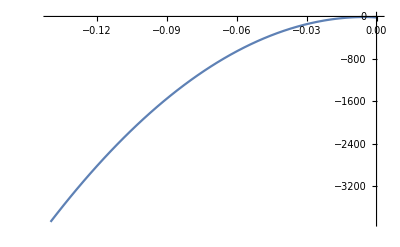

```mathematica
Plot[-(-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^2], {n, -0.14, 0.0004}]
```

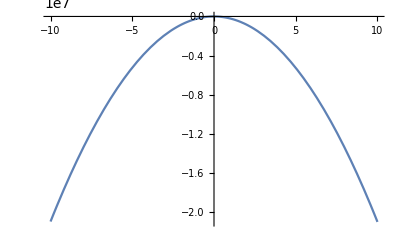

```mathematica
Plot[-(-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^2], {n, -10, 10}]
```

```mathematica
Log[0]
```

-∞

```mathematica
ClearAll[n, n2]
a = 9806.5;
b = 9807;
s1 = 9806.5;
s2 = 9806.5;
σ = 0.6;
τ = 5/(365*24*60); 
qwe = List[];For[n=1, n≤10, n++, AppendTo[qwe, -(-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)]]
qwe
```

{-52560.,-210240.,-473040.,-840960.,-1.314×10^6,-1.89216×10^6,-2.57544×10^6,-3.36384×10^6,-4.25736×10^6,-5.256×10^6}

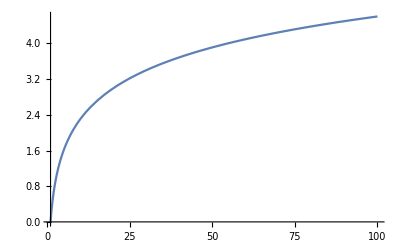

```mathematica
Plot[Log[x], {x, 1, 100}]
```

```mathematica
n in both case = nMin
```

```mathematica
ClearAll[s1,s2,a,b,σ, τ]
lPdf[s1_,s2_,a_,b_,nMin_,nMax_] = -1/2 (-κ-((-s2+θ) κ-σ^2/4)/(2 s2)+(((-s2+θ) κ-σ^2/4)^2)/(s2 σ^2)) τ+1/2 (-(2 s1 κ)/σ^2-Log[(2 √s1)/σ]+(4 θ κ Log[(2 √s1)/σ])/σ^2)+1/2 ((2 s2 κ)/σ^2+Log[(2 √s2)/σ]-(4 θ κ Log[(2 √s2)/σ])/σ^2)(Log[4/τ](-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^2]- (-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2])) )]) -Log[16a^2/τ^2](-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^4]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^4]- (-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^4])) )])+Log[16a*b/τ^2](-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^4]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^4]- (-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^4])) )])-Log[16a*Sqrt[s1]/(τ^2*σ)](-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^3]- (-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3])) )])+Log[16a*Sqrt[s2]/(τ^2*σ)](-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^3]- (-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3])) )])+Log[16a*b/τ^2](-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^4]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^4]- (-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^4])) )])-Log[16b^2/τ^2](-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^4]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^4]- (-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^4])) )])+Log[16b*Sqrt[s1]/(τ^2*σ)](-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^3]- (-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3])) )])-Log[16b*Sqrt[s2]/(τ^2*σ)](-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^3]- (-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3])) )])-Log[16a*Sqrt[s1]/(τ^2*σ)](-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^3]- (-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3])) )])+Log[16b*Sqrt[s1]/(τ^2*σ)](-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^3]- (-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3])) )])-Log[16s1/(τ^2*σ^2)](-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^2]- (-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2])) )])+Log[16Sqrt[s2]*Sqrt[s1]/(τ^2*σ^2)](-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^2]- (-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2])) )])+Log[16a*Sqrt[s2]/(τ^2*σ)](-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^3]- (-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3])) )])-Log[16b*Sqrt[s2]/(τ^2*σ)](-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^3]- (-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3])) )])+Log[16Sqrt[s2]*Sqrt[s1]/(τ^2*σ^2)](-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^2]- (-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2])) )])-Log[16s2/(τ^2*σ^2)](-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^2]- (-(-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2])) )])-(-Log[4/τ](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin])) )])+Log[4/τ](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^2]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2])) )])+Log[16a^2/τ^2](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin])) )])-Log[16a^2/τ^2](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^2]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2])) )])+Log[16a*b/τ^2](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^2]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2])) )])-Log[16a*Sqrt[s1]/(τ^2*σ)](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin])) )])+Log[16a*Sqrt[s2]/(τ^2*σ)](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin])) )])-Log[32a^2/τ^2](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^2]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2])) )])+Log[32a^2/τ^2](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^3]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3])) )])-Log[32a*b/τ^2](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^3]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3])) )])+Log[32a*Sqrt[s1]/(τ^2*σ)](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^2]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2])) )])-Log[32a*Sqrt[s2]/(τ^2*σ)](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^2]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2])) )])+Log[16a*b/τ^2](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^2]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2])) )])-Log[16a*b/τ^2](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^3]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3])) )])+Log[16b^2/τ^2](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^3]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3])) )])-Log[16b*Sqrt[s1]/(τ^2*σ)](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^2]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2])) )])+Log[16b*Sqrt[s2]/(τ^2*σ)](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^2]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2])) )])+Log[16a^2/τ^2](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^3]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3])) )])-Log[16a^2/τ^2](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^4]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^4]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^4])) )])+Log[16a*b/τ^2](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^4]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^4]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^4])) )])-Log[16a*Sqrt[s1]/(τ^2*σ)](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^3]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3])) )])+Log[16a*Sqrt[s2]/(τ^2*σ)](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^3]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3])) )])-Log[16a*b/τ^2](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^3]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3])) )])+Log[16a*b/τ^2](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^4]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^4]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^4])) )])-Log[16b^2/τ^2](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^4]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^4]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^4])) )])+Log[16b*Sqrt[s1]/(τ^2*σ)](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^3]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3])) )])-Log[16b*Sqrt[s2]/(τ^2*σ)](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^3]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3])) )])-Log[16a*Sqrt[s1]/(τ^2*σ)](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin])) )])+Log[16a*Sqrt[s1]/(τ^2*σ)](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^2]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2])) )])-Log[16b*Sqrt[s1]/(τ^2*σ)](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^2]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2])) )])+Log[16s1/(τ^2*σ^2)](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin])) )])-Log[16Sqrt[s1]*Sqrt[s2]/(τ^2*σ^2)](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin])) )])+Log[16a*Sqrt[s1]/(τ^2*σ)](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^2]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2])) )])-Log[16a*Sqrt[s1]/(τ^2*σ)](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^3]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3])) )])+Log[16b*Sqrt[s1]/(τ^2*σ)](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^3]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3])) )])-Log[16s1/(τ^2*σ^2)](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^2]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2])) )])+Log[16Sqrt[s1]*Sqrt[s2]/(τ^2*σ^2)](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^2]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2])) )])+Log[16a*Sqrt[s2]/(τ^2*σ)](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin])) )])-Log[16a*Sqrt[s2]/(τ^2*σ)](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^2]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2])) )])+Log[16b*Sqrt[s2]/(τ^2*σ)](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^2]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2])) )])-Log[16Sqrt[s1]*Sqrt[s2]/(τ^2*σ^2)](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin])) )])+Log[16s2/(τ^2*σ^2)](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin])) )])-Log[16a*Sqrt[s2]/(τ^2*σ)](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^2]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2])) )])+Log[16a*Sqrt[s2]/(τ^2*σ)](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^3]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3])) )])-Log[16b*Sqrt[s2]/(τ^2*σ)](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^3]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^3])) )])+Log[16Sqrt[s1]*Sqrt[s2]/(τ^2*σ^2)](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^2]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2])) )])-Log[16s2/(τ^2*σ^2)](-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2]+Log[∑_(n=nMin)^nMax (ⅇ^(-(-2a-2 (-a+b) n+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[n^2]- (-(-2a-2 (-a+b) nMin+(2 √s1)/σ-(2 √s2)/σ)^2/(2 τ)+Log[nMin^2])) )])))
```

FactorSquareFree::lrgexp: Exponent is out of bounds for function FactorSquareFree.

General::stop: Further output of FactorSquareFree::lrgexp will be suppressed during this calculation.

1/2 (-5.32621-21147.2 κ+59.1801 θ κ)+(κ+0.000131354 (-0.09+(-3806.5+θ) κ)-0.000729746 (-0.09+(-3806.5+θ) κ)^2)/210240+1/2 (5.32621+21147.2 κ-59.1801 θ κ) (0.+7.10543×10^-15 (-52560 (-7613.-1. nMin)^2+Log[nMin^4]+Log[∑_(n=nMin)^nMax (ⅇ^(-52560 (-7613.-1. n)^2+52560 (-7613.-1. nMin)^2) n^4)/nMin^4])-7.10543×10^-15 (-52560 (0.-1. nMin)^2+Log[nMin^4]+Log[∑_(n=nMin)^nMax (ⅇ^(-52560 (0.-1. n)^2+52560 (0.-1. nMin)^2) n^4)/nMin^4])+0.000131346 (-52560 (-7613.-1. nMin)^2+Log[nMin^3]+Log[∑_(n=nMin)^nMax (ⅇ^(-52560 (-7613.-1. n)^2+52560 (-7613.-1. nMin)^2) n^3)/nMin^3])-12.2563 (-52560 (-7613.-1. nMin)^2+Log[nMin^2]+Log[∑_(n=nMin)^nMax (ⅇ^(-52560 (-7613.-1. n)^2+52560 (-7613.-1. nMin)^2) n^2)/nMin^2])+12.9492 (-52560 (0.-1. nMin)^2+Log[nMin^2]+Log[∑_(n=nMin)^nMax (ⅇ^(-52560 (0.-1. n)^2+52560 (0.-1. nMin)^2) n^2)/nMin^2])-29.4381 (-52560 (-7613.-1. nMin)^2+Log[nMin]+Log[∑_(n=nMin)^nMax (ⅇ^(-52560 (-7613.-1. n)^2+52560 (-7613.-1. nMin)^2) n)/nMin]))